# Useful functions

```mathematica
makeSystem[var_, vart_, sys_]:= Module[{v, vt, S, St, Sf},
v = var;
vt = vart;
S = sys;
(St = S/.Thread[v-> vt]; Sf = Thread[D[vt, t] == St])]
```

```mathematica
FollowRoot[system_,commonpars_,followPar_,range_,variables_, initialEq_]:=Module[{sys,cpar,fp, r,v,en, ieq, eq, pars, results},sys=system;cpar=commonpars;fp=followPar;r = range;v=variables;
ieq = initialEq;
results={};
Do[eq=ieq;
pars = Join[cpar, {fp-> i}];
ieq = FindRoot[Thread[sys == ConstantArray[0, Length[v]]]/.pars,Thread[{v, v/.ieq}]];
results = AppendTo[results, ieq], {i, range}];
results];
```

```mathematica
StableMark[jacobmatrix_, parcommon_, parfollow_, equilibrium_]:=
Module[{jmat, pc, pf, r,eq, eiv, anyZero, anyPos, allNeg},
jmat = jacobmatrix;
pc = parcommon;
pf = parfollow;
eq = equilibrium;
eiv = Eigenvalues[jmat/.pc/.pf/.eq];
anyZero = AnyTrue[Thread[-10^-10<=Re[eiv]<=10^-10], TrueQ];
anyPos = AnyTrue[Thread[Re[eiv]>10^-10], TrueQ];
allNeg = AllTrue[Thread[Re[eiv]<-10^-10], TrueQ];
Which[anyZero, "*",anyPos, "*", allNeg, "."]]
```

```mathematica
ListMark[jacobmatrix_, parcommon_, parfollow_, range_,equiList_]:=
Module[{jmat, pc, pf, r,eql, eiv},
jmat = jacobmatrix;
pc = parcommon;
pf = parfollow;
r=range;
eql = equiList;
MapThread[StableMark,{ConstantArray[jmat, Length[eql]], ConstantArray[pc, Length[eql]],Thread[pf->r], eql}]]
```

# Single infection with trophical transmission

## Ecological dynamics of a resident

```mathematica
dIsdt = R[Iw, Is]- d Is- Π0[Ds, Dw] Is  - γw W Is ;(*Susceptible intermediate*)
dIwdt =  γw W Is  - (d + α)Iw - Π1[Ds, Dw, βw]Iw; (*Infected intermediate*)
dDsdt =B[Ds, Dw, Is, Iw]  - μ Ds - λ[βw, Iw] Ds;  (*Susceptible definitive*)
dDwdt =λ[βw, Iw] Ds- (μ + σ) Dw ;(*Infected definitive*)
dWdt = fw Dw - δ W - γw W Is;
```

```mathematica
func0 = {R[Iw, Is] -> r(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
func1 =  {R[Iw, Is] -> r(1- (Is + Iw)/Κ)(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
var = {Is, Iw, Ds, Dw, W};
vart = {Is[t], Iw[t], Ds[t], Dw[t], W[t]};
sys = {dIsdt, dIwdt, dDsdt, dDwdt, dWdt};
```

```mathematica
solW0 = Solve[Thread[sys == 0]/.func0/.W-> 0,{Is, Iw, Ds, Dw}]
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-d+r)/ρ,Dw→0}}

```mathematica
solW0Func1= Solve[Thread[sys == 0]/.func1/.W-> 0,{Is, Iw, Ds, Dw}]//FullSimplify
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→Κ-(d Κ)/r,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-r μ+c (-d+r) Κ ρ)/(c Κ ρ^2),Dw→0}}

Stability of the equilibrium

## Linear functions

```mathematica
A = {{r - d - Π0[Ds, Dw] - γw W, r, 0, 0, 0}, {γw W, - (d + α)-  Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
A//MatrixForm
```

(-d+r-W γw-Π0[Ds,Dw] | r | 0 | 0 | 0
W γw | -d-α-Π1[Ds,Dw,βw] | 0 | 0 | 0
0 | 0 | -Iw βw-μ+c (Is+Iw) ρ | c (Is+Iw) ρ | 0
0 | 0 | Iw βw | -μ-σ | 0
0 | 0 | 0 | fw | -Is γw-δ)

```mathematica
(A.var /.func0)== (sys/.func0)//FullSimplify
```

True

```mathematica
Aeigens = Eigenvalues[A/.func0]//FullSimplify;
```

```mathematica
FullSimplify[Aeigens/.solW0[[1]]/.W-> 0, Assumptions->{α>0, r>0, σ>0}]
```

{-δ,-d-α,-d+r,-μ-σ,-μ}

```mathematica
FullSimplify[Aeigens/.solW0[[2]]/.W-> 0, Assumptions->{r>0, d>0,μ>0, σ>0, ρ>0, α>0, βw>0}]
```

{-δ-(γw μ)/(c ρ),-(-d βw+r βw+(r+α) ρ+Abs[-d βw+r βw+(r+α) ρ])/(2 ρ),Piecewise[{{(d βw-α ρ-r (βw+ρ))/ρ, d βw>α ρ+r (βw+ρ)}, {0, True}}],-μ-σ,0}

## Logistic growth intermediate hosts

```mathematica
AFunc1 = {{r(1-(Is + Iw)/Κ) - d - Π0[Ds, Dw]-  γw W, r(1-(Is + Iw)/Κ), 0, 0, 0}, {γw W, - (d + α)- Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
(AFunc1/.func1).var == (sys/.func1)//FullSimplify
```

True

```mathematica
AeigensFunc1 = Eigenvalues[AFunc1/.func1]//FullSimplify
```

{-Is γw-δ,-1/(2 Κ)(Is r+Iw r+√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),-1/(2 Κ)(Is r+Iw r-√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ-√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2)),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ+√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2))}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[2]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d, (c p (-d+r) Κ+r σ)>0}]
```

{-δ+((d-r) γw Κ)/r,-d-α,0,-(c p (d-r) Κ+r (2 μ+σ)+Abs[c p (-d+r) Κ+r σ])/(2 r),(c p (-d+r) Κ-r (2 μ+σ)+Abs[c p (-d+r) Κ+r σ])/(2 r)}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[3]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d,  c> 0, μ+σ>0, p>0}]
```

{-δ-(γw μ)/(c p),-(c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ+√((c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ)^2))/(2 c p^2 Κ),(-c p (p (r+α)+(-d+r) βw) Κ+r (p+βw) μ+√((c p (p (r+α)+(-d+r) βw) Κ-r (p+βw) μ)^2))/(2 c p^2 Κ),-μ-σ,0}

Numerical analysis

```mathematica
sysFunc0 = makeSystem[var,vart ,  sys/.func0];
sysFunc1 = makeSystem[var,vart ,  sys/.func1];
```

```mathematica
prEco = {r -> 1.5, d -> 1.1, ρ -> 1.2,γw -> 4.5, α-> 0, βw-> 2.5, c-> 0.4, μ-> 1.9, σ-> 0, fw -> 14.5, δ-> 1.9};
```

```mathematica
maxt = 100;
initFunc0= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 30 };
NSolve[Thread[(sys/.func0/.prEco) == 0], var];
ndsol0Func0 = NDSolve[Join[sysFunc0/.prEco, initFunc0], var, {t, 0, maxt}]
```

NDSolve::ndsz: At t == 55.1567, step size is effectively zero; singularity or stiff system suspected.

{{Is→InterpolatingFunction[{{0., 55.1567}}, <>],Iw→InterpolatingFunction[{{0., 55.1567}}, <>],Ds→InterpolatingFunction[{{0., 55.1567}}, <>],Dw→InterpolatingFunction[{{0., 55.1567}}, <>],W→InterpolatingFunction[{{0., 55.1567}}, <>]}}

```mathematica
Plot[Evaluate[vart/.ndsol0Func0], {t, 0, maxt}, PlotRange->All, PlotLegends->{"Is", "Iw", "Ds", "Dw", "W"}]
```

-Graphics-

```mathematica
prEcoFunc1 = {r -> 4.5, d -> 1.1, ρ-> 0.5,γw -> 5.5, α-> 0, βw-> 1.5, c-> 0.4, μ-> 0.9, σ-> 0, fw -> 14.5, δ-> 9.9, Κ-> 50};
maxt = 700;
initFunc1= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 100 };
NSolve[Thread[(sys/.func1/.prEcoFunc1) == 0], var]
ndsol0Func1 = NDSolve[Join[sysFunc1/.prEcoFunc1, initFunc1], var, {t, 0, maxt}]
```

{{Is→-1.8,Iw→39.5778,Ds→0.,Dw→0.,W→-4.39753},{Is→37.7778,Iw→0.,Ds→0.,Dw→0.,W→0.},{Is→38.3778,Iw→-0.6,Ds→0.0476521,Dw→-0.0476521,W→-0.00312681},{Is→-3.71631,Iw→8.21631,Ds→0.0629334,Dw→0.8618,W→-1.18562},{Is→2.01854,Iw→2.48146,Ds→0.439411,Dw→1.8173,W→1.25468},{Is→4.5,Iw→0.,Ds→5.99,Dw→0.,W→0.},{Is→0.6,Iw→-0.6,Ds→0.182069,Dw→-0.182069,W→-0.2},{Is→-1.8,Iw→1.8,Ds→0.,Dw→0.,W→-0.2},{Is→27.3341,Iw→-22.8341,Ds→0.0113651,Dw→-0.432521,W→-0.0391391},{Is→0.,Iw→0.,Ds→0.,Dw→0.,W→0.}}

{{Is→InterpolatingFunction[{{0., 700.}}, <>],Iw→InterpolatingFunction[{{0., 700.}}, <>],Ds→InterpolatingFunction[{{0., 700.}}, <>],Dw→InterpolatingFunction[{{0., 700.}}, <>],W→InterpolatingFunction[{{0., 700.}}, <>]}}

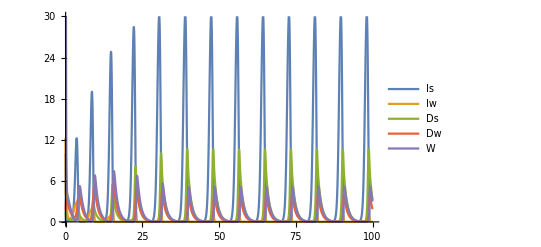

```mathematica
Plot[Evaluate[vart/.ndsol0Func1], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 30}}, PlotLegends->{"Is", "Iw", "Ds","Dw", "W"}]
```

## Mutant dynamics

```mathematica
dImudt = γm M Is  - (d + α)Imu -(Ds+Dw) (ρ+βm)Imu; (*Infected intermediate*)
dDmdt = Imu βm Ds - (μ + σ)Dm;
dMdt = fm Dm - δ M - γm Is M;
```

```mathematica
dMdt > 0
```

```mathematica
Am = {{-d-α - (Ds+Dw) (ρ+βm), 0, γm Is},{βm Ds, -μ -σ, 0},{0, fm, -δ- γm Is}};
Am//MatrixForm
```

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
Am.{Imu, Dm, M} == {dImudt, dDmdt, dMdt}//FullSimplify
```

True

```mathematica
FMat = {{0, 0, 0},{0, 0, 0}, {0, fm, 0}};
```

```mathematica
VMat ={{d+α+(Ds+Dw) (ρ+βm), 0, - Is γm},{-Ds βm, μ + σ, 0}, {0, 0, Is γm + δ}};
```

```mathematica
FMat - VMat == Am//FullSimplify
FMat-VMat//MatrixForm
```

True

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
R0 = Eigenvalues[FMat.Inverse[VMat]][[3]]//FullSimplify
```

(Ds fm Is βm γm)/((Is γm+δ) (d+α+(Ds+Dw) (βm+ρ)) (μ+σ))

R0=fm/(Is γm+δ)(Is  γm)/(d+α+(Ds+Dw) (ρ+βm))(Ds  βm)/(μ+σ)

# Double infections

## ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Π0[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Π1[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Π2[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + (1-q)λww) Ds- (μ + σw) Dw - ((1-q)λww +λw)Dw;
dDwwdt = q λww Ds + ((1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
```

## Predator and transmission functions

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Π0[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Π1[Ds, Dw,Dww, βw]-> (ρ + βw)(Ds + Dw+Dww),Π2[Ds, Dw,Dww, βww]-> (ρ + βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
func1 = {R[Iw, Is, Iww] -> r(1- (Is + Iw+Iww)/Κ)(Is + Iw+Iww), Π0[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Π1[Ds, Dw,Dww, βw]-> (ρ + βw)(Ds + Dw+ Dww),Π2[Ds, Dw, Dww, βww]-> (ρ + βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
```

## Simple analytical results

```mathematica
pFreeCond = {W-> 0, Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0};
pDFreeCond = { Dw-> 0, Dww-> 0};
```

Solution where both the intermediate and definitive hosts are free of parasites:

```mathematica
solRes0 = Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func0/.forceInf/.pFreeCond, varRes]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Ds→0},{Is→μ/(c ρ),Ds→-(d-r)/ρ}}

Solution where infected definitive hosts do not exist (Note this solution is not biologically meaningful because I_s is always negative):

```mathematica
solResD0 =  Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func0/.forceInf/.pDFreeCond, varRes]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Iw→0,Iww→0,Ds→0,W→0},{Is→-δ/γ,Iw→-((-1+p) (d-r) (d+αww) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Iww→(p (d-r) (d+αw) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Ds→0,W→-((d-r) (d+αw) (d+αww))/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ)},{Is→μ/(c ρ),Iw→0,Iww→0,Ds→(-d+r)/ρ,W→0}}

## Stability of equilibrium

```mathematica
Jmat = D[odesRes/.func0/.forceInf, {varRes}];
```

```mathematica
Jmat/.solRes0[[2]]/.pFreeCond//MatrixForm
eivPF = Eigenvalues[%]//FullSimplify
```

(0 | r | r | -μ/c | -μ/c | -μ/c | -(γ μ)/(c ρ)
0 | -d-αw+((d-r) (βw+ρ))/ρ | 0 | 0 | 0 | 0 | ((1-p) γ μ)/(c ρ)
0 | 0 | -d-αww+((d-r) (βww+ρ))/ρ | 0 | 0 | 0 | (p γ μ)/(c ρ)
-c (d-r) | -c (d-r)+((d-r) βw)/ρ | -c (d-r)+((d-r) βww)/ρ | 0 | μ | μ | 0
0 | -((d-r) βw)/ρ | -((1-q) (d-r) βww)/ρ | 0 | -μ-σw | 0 | 0
0 | 0 | -(q (d-r) βww)/ρ | 0 | 0 | -μ-σww | 0
0 | 0 | 0 | 0 | fw | fww | -δ-(γ μ)/(c ρ))

{-√(d-r) √μ,√(d-r) √μ,Root[1&,1]/(c ρ^5),Root[1&,2]/(c ρ^5),Root[1&,3]/(c ρ^5),Root[-c^4 d^2 fw βw βww γ μ^2 ρ^22+250+#1^5&,4]/(c ρ^5),Root[-c^4 d^2 fw βw βww γ μ^2 ρ^22+250+#1^5&,5]/(c ρ^5)}
 |  |  |  |

```mathematica
Jmat/.Thread[varRes-> 0]//MatrixForm
eivExtinct = Eigenvalues[%]//FullSimplify
```

(-d+r | r | r | 0 | 0 | 0 | 0
0 | -d-αw | 0 | 0 | 0 | 0 | 0
0 | 0 | -d-αww | 0 | 0 | 0 | 0
0 | 0 | 0 | -μ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ-σw | 0 | 0
0 | 0 | 0 | 0 | 0 | -μ-σww | 0
0 | 0 | 0 | 0 | fw | fww | -δ)

{-d+r,-d-αw,-d-αww,-δ,-μ,-μ-σw,-μ-σww}

## Numerical results func0 (linear functions)

## General view

```mathematica
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

```mathematica
sys = makeSystem[varRes, vartRes, odesRes/.func0/.forceInf];
sysfunc0 = odesRes/.forceInf/.func0;
```

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.8,r -> 2.5, γ -> 0.1, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9};
```

```mathematica
AbsoluteTiming[Solve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes] ]
```

$Aborted

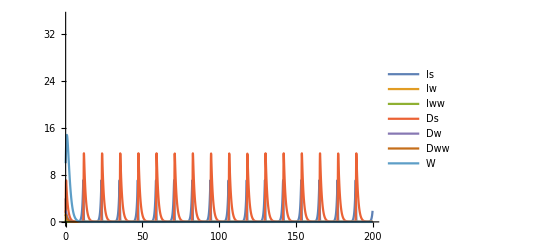

```mathematica
maxt = 200;
init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};
sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sys/.prEco0, init0], varRes, {t, 0, maxt}] ;
Plot[Evaluate[vartRes/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 35}}, PlotLegends->{"Is", "Iw", "Iww", "Ds", "Dw", "Dww", "W"}]
```

{{1.31028×10^-54,1.45586×10^-55,1.71114×10^-55,1.71285×10^-58,1.24683×10^-53}}

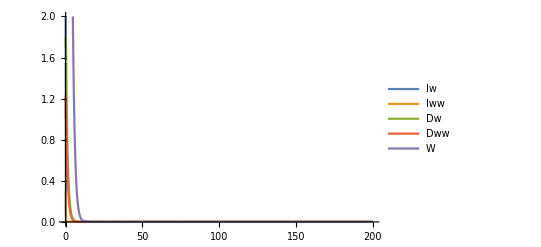

```mathematica
Evaluate[{Iw[maxt], Iww[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsol0]
Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 2}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}]
```

## Bifurcation parameter γ

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};;
γrange = Range[0.1, 8, 0.05];
```

```mathematica
solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
```

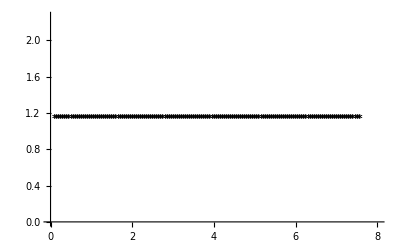

```mathematica
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};
eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγzero], PlotStyle-> Black];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγzero], PlotStyle-> Gray];
Show[p0, p1]
```

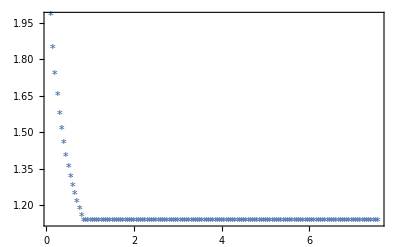

```mathematica
colordata = ColorData[97, "ColorList"];
varname = Is;
eqγ1 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[1]]];
{#}& /@Transpose[{γrange, varname/.eqγ1}];
pγ1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ1], PlotStyle-> colordata[[1]]];
eqγ2 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[2]]];
{#}& /@Transpose[{γrange, varname/.eqγ2}];
pγ2 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ2], PlotStyle-> colordata[[2]]];
eqγ13 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[13]]];
{#}& /@Transpose[{γrange, varname/.eqγ13}];
pγ13 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ13], PlotStyle-> colordata[[3]]];
eqγ16 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[16]]];
{#}& /@Transpose[{γrange, varname/.eqγ16}];
pγ16 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ16], PlotStyle-> colordata[[4]]];
eqγ17 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[17]]];
{#}& /@Transpose[{γrange, varname/.eqγ17}];
pγ17 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ17], PlotStyle-> colordata[[5]]];
Show[pγ1, pγ2, pγ13,pγ16,pγ17,PlotRange-> All, Frame-> True, FrameLabel-> {"Infection rate of free parasite (γ)", "Density of population"}]
```

## Bifurcation parameter βw

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];
```

```mathematica
solsβw = NSolve[Thread[(odesRes/.func0/.forceInf/.parβw/.βw-> 1.5) == 0], varRes];
```

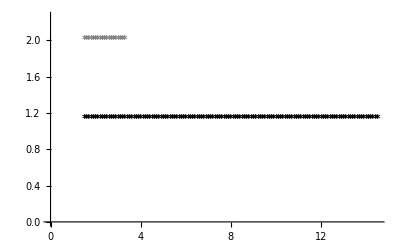

```mathematica
eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};
eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListMark[Jmat, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray];
Show[p0, p1]
```

## Mutant dynamics

```mathematica
2p (M W)/(M + W)^2+ p M^2/(M+W)^2+(1-p)W/(M + W)+(1-p)M/(M+W)+p W^2/(M + W)^2//FullSimplify
```

1

```mathematica
dImdt = (1-p)ηm Is - (d + αm) Imut - Π3[Ds, Dw,Dww, βm, Dm, Dmm, Dmw]Imut;
dImmdt = p ηmm Is - (d + αmm) Imm - Π4[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw]Imm;
dImwdt = p ηmw Is - (d + αmw) Imw - Π5[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw]Imw;
dDmdt =( λm + (1-q)(λmm + λmw))Ds - (μ + σm) Dm - (λw + (1-q)(λww + λmw))Dm;
dDmmdt = q λmm Ds + (λm + (1-q)(λmm + λmw))Dm -(μ + σmm)Dmm;
dDmwdt = q λmw Ds(λm + (1-q)(λmm + λmw))Dw + (λw + (1-q)(λww + λmw))Dm - (μ + σmw) Dmw;
dMdt = fm Dw + fmm Dm + fmw Dmw - δ M - (ηm + ηmw + ηmm)Is;
odesMut = {dImdt, dImwdt, dImmdt, dDmdt, dDmwdt, dDmmdt, dMdt};
varMut = {Imut,  Imm,Imw, Dm, Dmm, Dmw, M};
forceInfMut = {ηm -> γ M/(M+W)(M + W), ηmm ->γ M^2/(M+W)^2(M + W), ηmw ->  γ 2 (M W)/(M + W)^2(M + W), λm -> βm Imut, λmw -> βmw Imw, λmm -> βmm Imm, λw -> βw Iw, λww -> βww Iww};
```